# Superposition of two waves

## Play

```mathematica
Clear["Global`*"]
```

```mathematica
f[t_]=Sum[Sin[2π ν t],{ν,200,201}]
```

Sin[400 π t]+Sin[402 π t]

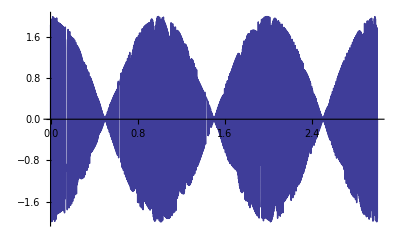

```mathematica
Plot[f[t],{t,0,3}]
```

```mathematica
play=Play[f[t],{t,0,10}]
```

-Graphics-

## Export

### Get current notebook directory

```mathematica
CurrentNotebookDirectory=NotebookDirectory[SelectedNotebook[]]
```

/Users/Soha/Google Drive/Café Planck/2-Physics/03-Sound waves/

### Set Directory to current notebook directory

```mathematica
SetDirectory[CurrentNotebookDirectory]
```

/Users/Soha/Google Drive/Café Planck/2-Physics/03-Sound waves

### Get current notebook name

```mathematica
CurrentNotebookName=StringTake[ToString[SelectedNotebook[]],{18,StringPosition[ToString[SelectedNotebook[]],">",1][[1,1]]-1}]
```

03-Superposition of two waves.nb

### Export

```mathematica
fileName=StringJoin[StringDrop[CurrentNotebookName,-3],".wav"];
```

```mathematica
Export[fileName,play];
```